```mathematica
Nstate=4
```

4

```mathematica
kini[p_] := {{-p-1,1,1,1},{p,-2,1,1},{1,1,-2,1},{1,1,1,-2}}
```

```mathematica
columnsum[p_]:= Total[kini[p],1]
```

```mathematica
columnsum[p]
```

{1,1,1,1}

```mathematica
diag[p_]:=DiagonalMatrix[Table[kini[p][[i,i]],{i,Nstate}]]
```

```mathematica
diag[p]// MatrixForm
```

(-1-p | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
escaperate[p_]:= Total[kini[p]-diag[p],1]
```

```mathematica
escaperate[p]//MatrixForm
```

(2+p
3
3
3)

```mathematica
DiagonalMatrix[escaperate[p]]//MatrixForm
```

(2+p | 0 | 0 | 0
0 | 3 | 0 | 0
0 | 0 | 3 | 0
0 | 0 | 0 | 3)

```mathematica
k[p_]:= kini[p]-diag[p]-DiagonalMatrix[escaperate[p]]
```

```mathematica
k[p]//MatrixForm
```

(-2-p | 1 | 1 | 1
p | -3 | 1 | 1
1 | 1 | -3 | 1
1 | 1 | 1 | -3)

```mathematica
colsum[p_]:= Total[k[p],1]
```

```mathematica
colsum[p]
```

{0,0,0,0}

```mathematica
{eigs, vecs} = Eigensystem[k[p]]
```

{{-4,-4,0,-3-p},{{0,-1,0,1},{0,-1,1,0},{4/(3+p),(2 (1+p))/(3+p),1,1},{-1,1,0,0}}}

```mathematica
eigs
```

{-4,-4,0,-3-p}

```mathematica
vecs
```

{{0,-1,0,1},{0,-1,1,0},{4/(3+p),(2 (1+p))/(3+p),1,1},{-1,1,0,0}}

```mathematica
pb [p_]:= {4/(3+p),(2 (1+p))/(3+p),1,1} 
Print[pb[p]//MatrixForm]
```

(4/(3+p)
(2 (1+p))/(3+p)
1
1)

```mathematica
Simplify[Total[pb[p]]]
```

4

```mathematica
prob[p_]:=pb[p]/4
```

```mathematica
prob[p]//MatrixForm
```

(1/(3+p)
(1+p)/(2 (3+p))
1/4
1/4)

```mathematica
j12 = Simplify[k[p][[1,2]]*prob[p][[2]]-k[p][[2,1]]prob[p][[1]]]
j13 = Simplify[k[p][[1,3]]prob[p][[3]]-k[p][[3,1]]prob[p][[1]]]
j13 = k[p][[1,3]]prob[p][[3]]-k[p][[3,1]]prob[p][[1]]
j13 = k[p][[1,3]]prob[p][[3]]-k[p][[3,1]]prob[p][[1]]
j13 = k[p][[1,3]]prob[p][[3]]-k[p][[3,1]]prob[p][[1]]
```

(1-p)/(6+2 p)

(-1+p)/(4 (3+p))

1/(2+4/(3+p)+(2 (1+p))/(3+p))-4/((3+p) (2+4/(3+p)+(2 (1+p))/(3+p)))

1/(2+4/(3+p)+(2 (1+p))/(3+p))-4/((3+p) (2+4/(3+p)+(2 (1+p))/(3+p)))

1/(2+4/(3+p)+(2 (1+p))/(3+p))-4/((3+p) (2+4/(3+p)+(2 (1+p))/(3+p)))

```mathematica
1-4/(3+p)
```

1-4/(3+p)

```mathematica
current[p_]:= Simplify[Table[k[p][[i,j]]prob[p][[j]]-k[p][[j,i]]prob[p][[i]],{i,4},{j,4}]]
```

```mathematica
Print[current[p]//MatrixForm]
```

(0 | (1-p)/(6+2 p) | 1/4-1/(3+p) | 1/4-1/(3+p)
(-1+p)/(2 (3+p)) | 0 | -(-1+p)/(4 (3+p)) | -(-1+p)/(4 (3+p))
-1/4+1/(3+p) | (-1+p)/(4 (3+p)) | 0 | 0
-1/4+1/(3+p) | (-1+p)/(4 (3+p)) | 0 | 0)

```mathematica
entkrix[p_] := Simplify[(1/2)*Table[current[p][[i,j]]Log[(k[p][[i,j]]prob[p][[j]])/(k[p][[j,i]]prob[p][[i]])],{i,4},{j,4}]]
systementkrix[p_]:=Simplify[(1/2)*Table[current[p][[i,j]]Log[(prob[p][[j]])/(prob[p][[i]])],{i,4},{j,4}]]
reservoirkrix[p_]:=Simplify[(1/2)*Table[current[p][[i,j]]Log[(k[p][[i,j]])/(k[p][[j,i]])],{i,4},{j,4}]]
```

```mathematica
Print["Total Entropy production matrix:"]
Print[entkrix[p]//MatrixForm]
Print["System Entropy Production Matrix: "]
Print[systementkrix[p]//MatrixForm]
Print["Reservoir Entropy Production Matrix"]
Print[reservoirkrix[p]//MatrixForm]
```

Total Entropy production matrix:

(0 | -((-1+p) Log[(1+p)/(2 p)])/(4 (3+p)) | ((-1+p) Log[(3+p)/4])/(8 (3+p)) | ((-1+p) Log[(3+p)/4])/(8 (3+p))
((-1+p) Log[(2 p)/(1+p)])/(4 (3+p)) | 0 | -((-1+p) Log[(3+p)/(2+2 p)])/(8 (3+p)) | -((-1+p) Log[(3+p)/(2+2 p)])/(8 (3+p))
-((-1+p) Log[4/(3+p)])/(8 (3+p)) | ((-1+p) Log[(2 (1+p))/(3+p)])/(8 (3+p)) | 0 | 0
-((-1+p) Log[4/(3+p)])/(8 (3+p)) | ((-1+p) Log[(2 (1+p))/(3+p)])/(8 (3+p)) | 0 | 0)

System Entropy Production Matrix:

(0 | -((-1+p) Log[(1+p)/2])/(4 (3+p)) | ((-1+p) Log[(3+p)/4])/(8 (3+p)) | ((-1+p) Log[(3+p)/4])/(8 (3+p))
((-1+p) Log[2/(1+p)])/(4 (3+p)) | 0 | -((-1+p) Log[(3+p)/(2+2 p)])/(8 (3+p)) | -((-1+p) Log[(3+p)/(2+2 p)])/(8 (3+p))
-((-1+p) Log[4/(3+p)])/(8 (3+p)) | ((-1+p) Log[(2 (1+p))/(3+p)])/(8 (3+p)) | 0 | 0
-((-1+p) Log[4/(3+p)])/(8 (3+p)) | ((-1+p) Log[(2 (1+p))/(3+p)])/(8 (3+p)) | 0 | 0)

Reservoir Entropy Production Matrix

(0 | -((-1+p) Log[1/p])/(4 (3+p)) | 0 | 0
((-1+p) Log[p])/(4 (3+p)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(*Check whether entkrix = systemkrix+reserkrix*)
```

```mathematica
Print[FullSimplify[entkrix[p]==systementkrix[p]+reservoirkrix[p],p>0]]
```

True

```mathematica
entrate[p_] := Simplify[Total[entkrix[p],2],p>0]
systementrate[p_]:=Simplify[Total[systementkrix[p],2],p>0]
reservoientrate[p_]:=Simplify[Total[reservoirkrix[p],2],p>0]
```

```mathematica
Print[entrate[p]]
Print[systementrate[p]]
Print[reservoientrate[p]]
```

((-1+p) Log[p])/(2 (3+p))

0

((-1+p) Log[p])/(2 (3+p))

```mathematica
entrate[3]
```

Log[3]/6

```mathematica
Simplify[entrate[p],p>0]
```

((-1+p) Log[p])/(2 (3+p))

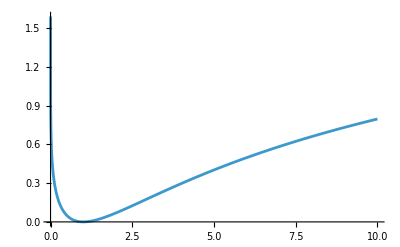

```mathematica
Plot[entrate[p],{p,0,10}]
```

```mathematica
entrate[3]
```

2/3 Log[4/3]+4/3 Log[3/2]

```mathematica
k[3]//MatrixForm
```

(-5 | 1 | 1 | 1
3 | -3 | 1 | 1
1 | 1 | -3 | 1
1 | 1 | 1 | -3)

```mathematica
(*Properties of the Jump states*)
```

```mathematica
Print["Transition rate Matrix: "]
Print[k[p]//MatrixForm]
Print["Steady state Probability: "]
Print[prob[p]//MatrixForm]
Print["Steady State Current Matrix of the form J[i,j]: "]
Print[current[p]//MatrixForm]
Print["Total Entropy Production rate: ", entrate[p]]
```

Transition rate Matrix:

(-2-p | 1 | 1 | 1
p | -3 | 1 | 1
1 | 1 | -3 | 1
1 | 1 | 1 | -3)

Steady state Probability:

(1/(3+p)
(1+p)/(2 (3+p))
1/4
1/4)

Steady State Current Matrix of the form J[i,j]:

(0 | (1-p)/(6+2 p) | 1/4-1/(3+p) | 1/4-1/(3+p)
(-1+p)/(2 (3+p)) | 0 | -(-1+p)/(4 (3+p)) | -(-1+p)/(4 (3+p))
-1/4+1/(3+p) | (-1+p)/(4 (3+p)) | 0 | 0
-1/4+1/(3+p) | (-1+p)/(4 (3+p)) | 0 | 0)

Total Entropy Production rate: ((-1+p) Log[p])/(2 (3+p))